# Cosmology Calculator

```mathematica
Clear["Global`*"];
pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]
```

-Graphics-

```mathematica
(*scale factor in terms of the Redshift  *)
scalfactor[z_]:=1/(1+z);
redshift[a_]:=1/a-1;
```

-Graphics-

```mathematica
(*Function to compute conformal time for a given redshift*)
tau[zs_,H0_,Ωm_,Ωd_,w_,Ωr_]:=NIntegrate[H0^-1/(√(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)),{z,zs,∞},PrecisionGoal->12,AccuracyGoal->12]
```

-Graphics-

```mathematica
(*Function to compute Physical time for a given redshift = (a'(tau))/a*)
time[zs_,H0_,Ωm_,Ωd_,w_,Ωr_]:=NIntegrate[H0^-1/((1+z)√(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)),{z,zs,∞}]
```

Friedmann equation: (FROM https://en.wikipedia.org/wiki/Hubble%27s_law)

-Graphics-

```mathematica
(*Physical Hubble Function at a given redshift = (ȧ)/a *)
PhysicalHubble[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(3(1+w)) +Ωm (1+z)^3+Ωr(1+z)^4)
```

```mathematica
(*Conformal Hubble Function at a given redshift *)
ConformalHubble[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=H0 √(Ωd(1+z)^(1+3 w) +Ωm (1+z)+Ωr(1+z)^2)
```

```mathematica
(*Time derivative of the Conformal Hubble Function at a given redshift = (ȧ)/a *)
ConformalHubblePrime[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=D[ConformalHubble[z,H0,Ωm,Ωd,w,Ωr],z]*(-(1+z)^2)*ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]*1/(1+z);  (* (d HH)/dtau = dH/dz  dz/da da/dtau*)
```

```mathematica
(*(*Physical Hubble Function at a given redshift = (ȧ)/a *)
ConformalHubblePrimePrime[z_,H0_,Ωm_,Ωd_,w_,Ωr_]:=D[ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr],z]*D[1/a-1,a]*ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]*1/(1+z);  (* (d ^2HH)/dtau^2 = dH/dz  dz/da da/dtau*)*)
```

The equation to find a’’(\tau) which must be consistent with what we find previously. We don’t need to do it, instead we can just

Where for when we don’t have radiation:

-Graphics-

Here we neglect pressure from radiation, meaning that we don' t go deep to the radiation domination and we start our equations from z = 1000 for example

```mathematica
(*Here we neglect pressure from radiation, meaning that we don't go deep to the radiation domination and we start our equations from z=1000 for example*)

dNlnH[NN_,H0_,Ωm_,Ωd_,w_]:= D[ Log[ConformalHubble[1/E^NN-1,H0,Ωm,Ωd,w,0]],NN](*N=ln a*)
Psiequation[ψ_,NN_,H0_,Ωm_,Ωd_,w_]:= ψ''[NN] +(3+ dNlnH[NN,H0,Ωm,Ωd,w])ψ'[NN]+(2-(3 Ωm)/(2 Ωm + 2 Ωd Exp[-3w NN])+dNlnH[NN,H0,Ωm,Ωd,w])ψ[NN]
```

Finding Ψ fom the Growth factor equation

-Graphics--Graphics-

-Graphics-

```mathematica
Growthequation = DD''[τ] +a'[τ]/a[τ] DD'[τ]+-3/2 Ωm (a'[τ]/a[τ])^2 DD[τ];
```

Substituting the ansatz and then see if the equation we get is similar

```mathematica
Block[{DD},DD[τ_]:=Ψ[τ]a[τ];Growthequation]==0 /.{a'[τ]->Η[τ] a[τ]}/.{a''[τ]->Η'[τ]a[τ] + Η[τ]^2 a[τ]}//Simplify
```

a[τ] ((-4+3 Ωm) Η[τ]^2 Ψ[τ]-6 Η[τ] Ψ'[τ]-2 (Ψ[τ] Η'[τ]+Ψ''[τ]))==0

RESULTS

τ :  with high accuracy

```mathematica
(* Cosmology setting *)
H0=0.0691023;Ωm=0.31;Ωr=9 10^-5; w=-1;Ωd=1-Ωm-Ωr;
NumberForm[tau[0,H0,Ωm,Ωd,w,Ωr],12]
(*Ωd*)
```

tau[0,0.0691023,0.31,0.68991,-1,9/100000]

0.68991

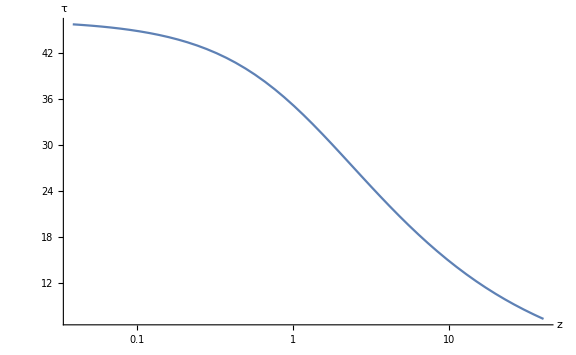

```mathematica
(* Cosmology setting *)
Ωd=0.687;H0=0.0691023;Ωm=0.31;Ωr=9 10^-5; w=-1;
LogLinearPlot[tau[z,H0,Ωm,Ωd,w,Ωr],{z,0,40},ImageSize->Large,PlotRange->All,AxesLabel->{"z","τ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

The formula for \HH(z)

-Graphics-

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]//pdConv
```

H0 √(Ωd (z+1)^(3 w+1)+Ωm (z+1)+Ωr (z+1)^2)

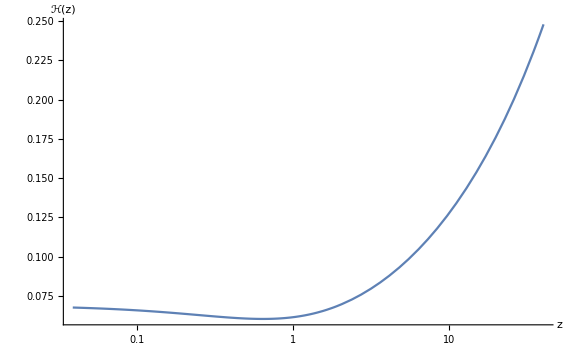

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Eq=ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1;
LogLinearPlot[Eq,{z,0,40},ImageSize->Large,PlotRange->All,AxesLabel->{"z","ℋ(z)"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Eq=ConformalHubble[z,H0,Ωm,Ωd,w,Ωr]/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1;
LogLinearPlot[Eq,{z,0,40},ImageSize->Large,PlotRange->All,AxesLabel->{"z","ℋ(z)"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

The formula for d \HH/dtau (z)

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr]//pdConv
```

-1/2 H0^2 (z+1) ((3 w+1) Ωd (z+1)^(3 w)+Ωm+2 Ωr (z+1))

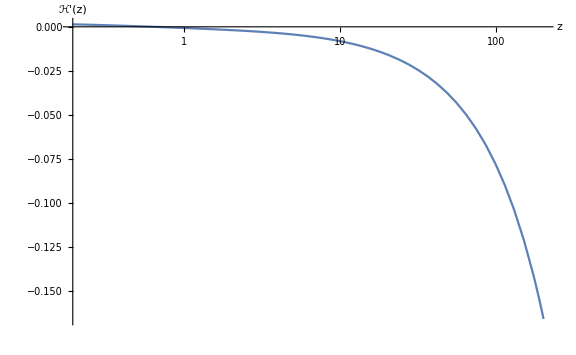

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Eq=ConformalHubblePrime[z,H0,Ωm,Ωd,w,Ωr]/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1;
LogLinearPlot[Eq,{z,0,200},ImageSize->Large,PlotRange->All,AxesLabel->{"z","ℋ'(z)"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

The formula for Ψ

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Sol = DSolve[(Psiequation[ψ,NN,H0,Ωm,Ωd,w]==0),ψ[NN], NN];
Print[Sol];
```

{{ψ[NN]→C[1] Hypergeometric2F1[1/2-1/(2 w),-1/(3 w),1-5/(6 w),-((ⅇ^-NN)^(3 w) Ωd)/Ωm]+((ⅇ^-NN)^(3 w))^(5/6/w) Ωd^(5/6/w) Ωm^(-5/6/w) C[2] Hypergeometric2F1[1/2+1/(3 w),1/(2 w),1+5/(6 w),-((ⅇ^-NN)^(3 w) Ωd)/Ωm]}}

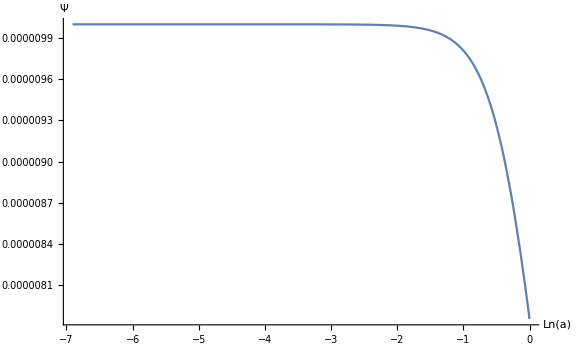

```mathematica
Clear["Ωm","Ωd","w","Ωr","H0"];
Plot[ψ[NN]/.Sol/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1/.C[1]->10^-5/.C[2]->0,{NN,Log[1/(1+1000)],Log[1/(1+0)]},ImageSize->Large,PlotRange->All,AxesLabel->{"Ln(a)","Ψ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

Numerical solution of Ψ

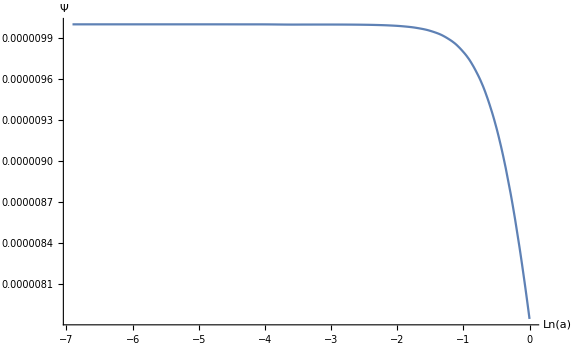

```mathematica
Solnumer = NDSolve[{(Psiequation[ψ,NN,H0,Ωm,Ωd,w]==0)/.Ωd->0.687 /.H0->0.0691023/.Ωm->0.31/.Ωr->9 10^-5/. w->-1,ψ[Log[1/(1+1000)]]==10^-5,ψ'[Log[1/(1+1000)]]==0},ψ,{NN,Log[1/(1+1000)],Log[1/(1+0)]}];
Plot[ψ[NN]/.Solnumer,{NN,Log[1/(1+1000)],Log[1/(1+0)]},ImageSize->Large,PlotRange->All,AxesLabel->{"Ln(a)","Ψ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

Checking whether at high z (early times) H(τ) behaves like 2/τ as expected

(to be discussed by FH)

```mathematica
Ωm= 3/10;ΩR = 0;w=-1;H0= 0.06927345697102467;
s = NDSolve[{(a'[tau] -a[tau]H0 √(ΩR a[tau]^-2 + Ωm a[tau]^-1+(1-Ωm)a[tau]^(-(1+3 w)))== 0),a[46]==1},a, {tau,0.01,46.3},Method->"ExplicitRungeKutta"]
```

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {-0.0692735 a[tau] √(3/10 Power[«2»]+7/10 Power[«2»])+a'[tau]==0,True}.

NDSolve[{-0.0692735 a[tau] √(3/(10 a[tau])+(7 a[tau]^2)/10)+a'[tau]==0,True},a,{tau,0.01,46.3},Method→ExplicitRungeKutta]

```mathematica
Plot[Evaluate[((a'[t]/.s)/(a[t]/.s))*(t-47)],{t,0.1,12.3},ImageSize->Large,PlotRange->All,AxesLabel->{"τ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

ReplaceAll::reps: {NDSolve[{-0.0692735 a[tau] √Plus[«2»]+a'[tau]==0,True},a,{tau,0.01,46.3},Method→ExplicitRungeKutta]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NDSolve::deqn: Equation or list of equations expected instead of True in the first argument {-0.0692735 a[tau] √(0.3 Power[«2»]+0.7 Power[«2»])+a'[tau]==0.,True}.

General::stop: Further output of NDSolve::deqn will be suppressed during this calculation.

-Graphics-

```mathematica
Ωm= 1;ΩR = 0;w=-1;H0= 0.06927345697102467;
s = NDSolve[{(a'[tau] -a[tau]^(-1/2)== 0),a[16]==1},a, {tau,0.0,12.3}]
```

{{a→InterpolatingFunction[…]}}

```mathematica
Ωm= 1;ΩR = 0;w=-1;H0= 0.06927345697102467;
news = DSolve[(a'[tau] -a[tau]^(-1/2)== 0),a, tau]
```

{{a→Function[{tau},(3/2)^(2/3) (tau+C[1])^(2/3)]}}

```mathematica
{{a->Function[{tau},(3/2)^(2/3) (tau+C[1])^(2/3)]}}
```

```mathematica
Solve[(3/2)^(2/3) (47+c)^(2/3)==1,c]//N
a'[t]/.news
```

{{c→-46.3333}}

{(2/3)^(1/3)/(t+C[1])^(1/3)}

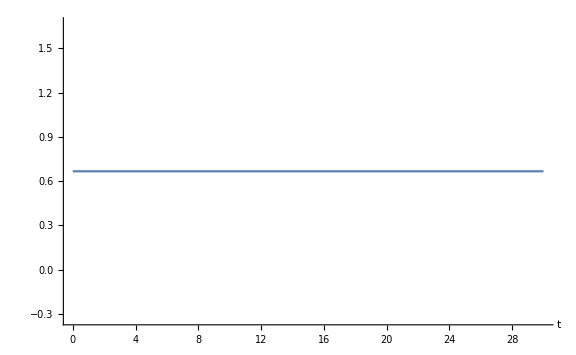

```mathematica
Plot[Evaluate[(((a'[t]/.news)/(a[t]/.news))/.C[1]->-46.333333333333336)*(t-46.333333333333336)],{t,0.0,30},ImageSize->Large,PlotRange->All,AxesLabel->{"t"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

```mathematica
Plot[Evaluate[((a'[t]/.news)/(a[t]/.news))*(t-47)],{t,0.1,12.3},ImageSize->Large,PlotRange->All,AxesLabel->{"τ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

```mathematica
Ωm= 1;ΩR = 0;w=-1;H0= 0.06927345697102467;
news = NDSolve[{(a'[tau] -a[tau]^(-1/2)== 0),a[47]==1},a, {tau,0.0,46.3}]
```

{{a→InterpolatingFunction[…]}}

```mathematica
Plot[a[tau]/.news,{tau,0.1,10.3},ImageSize->Large,PlotRange->All,AxesLabel->{"τ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

-Graphics-

```mathematica
Plot[Evaluate[((a'[tau]/.news)/(a[tau]/.news))],{tau,0.0,12.3},ImageSize->Large,PlotRange->All,AxesLabel->{"τ"},LabelStyle -> Directive[FontFamily -> "Arial", Black, FontSize -> 20]]
```

-Graphics-

PDE solving and finding ODE

```mathematica
(*Just to show the derivative in a traditional form*)
Clear["Global`*"];
pdConv[f_]:=TraditionalForm[f/.Derivative[inds__][g_][vars__]:>Apply[Defer[D[g[vars],##]]&,Transpose[{{vars},{inds}}]/.{{var_,0}:>Sequence[],{var_,1}:>{var}}]]

Eq2[t_,x_]:= D[pi[t,x], t,t]  - D[pi[t,x], x] D[pi[t,x], x] ;
Eq2[t,x]==0//pdConv
(∂^2 pi(t,x))/(∂t^2)-((∂pi(t,x))/(∂x))^2==0
assum2[t_,x_] := a[t] x^2;
NewEq2=Block[{pi},pi[t_,x_]:=assum2[t,x];Eq2[t,x]]
-4 x^2 a[t]^2+x^2 a''[t]
For[i=1,i<6,i++,Print[ToString[x^i,StandardForm]<>": ",Coefficient[NewEq2,x^i]]]
```

Solvind the full equation π^(..) +Lin=NL

```mathematica
(*Definition of Ψ and the linear term*)
Ψ[τ_,x_]:=ψ0[τ] +ψ1[τ] x + ψ2[τ] x^2 +ψ3[τ] x^3+ ψ4[τ] x^4;
(*L[t_,x_] := 2/t(1-3w)∂_t pi[t,x] + (-2/t^2-3w 4/t^2+3 cs2 6/t^2)pi[t,x]+6/t(w-cs2)Ψ[x]-cs2∂_(x,x) pi[t,x];*)
L[τ_,x_] := Subscript[l, πd][τ]D[pi[τ,x], τ] + Subscript[l, π][τ]pi[τ,x]+Subscript[l, Ψ][τ] Ψ[τ,x]+Subscript[l, Ψd][τ] D[Ψ[τ,x], τ]+Subscript[l, πpp][τ]D[pi[τ,x], x,x];

Print[L[τ,r]//pdConv]
Subscript[l, πpp](τ) (∂^2 pi(τ,r))/(∂r^2)+Subscript[l, πd](τ) (∂pi(τ,r))/(∂τ)+Subscript[l, π](τ) pi(τ,r)+Subscript[l, Ψ](τ) (r^4 ψ4(τ)+r^3 ψ3(τ)+r^2 ψ2(τ)+r ψ1(τ)+ψ0(τ))+Subscript[l, Ψd](τ) (r^4 (∂ψ4(τ))/(∂τ)+r^3 (∂ψ3(τ))/(∂τ)+r^2 (∂ψ2(τ))/(∂τ)+r (∂ψ1(τ))/(∂τ)+(∂ψ0(τ))/(∂τ))
(*Definition of non-linear term*)
NonLin[τ_,x_]:= Subscript[ν, πpπp][τ] (D[pi[τ,x], x])^2 +Subscript[ν, πpπpd][τ]D[pi[τ,x], x]D[pi[τ,x], τ,x] + Subscript[ν, ππpp][τ] pi[τ,x]D[pi[τ,x], x,x]+Subscript[ν, πdπpp][τ] D[pi[τ,x], τ] D[pi[τ,x], x,x]+Subscript[ν, Ψπpp][τ] Ψ[τ,x] D[pi[τ,x], x,x]+Subscript[ν, Ψpπp][τ] D[Ψ[τ,x], x]D[pi[τ,x], x]+Subscript[ν, πpπpπpp][τ](D[pi[τ,x], x])^2 D[pi[τ,x], x,x];
(*Printing non-linear terms and checked *)

Print[NonLin[τ,x]//pdConv];
```

The full equation without linear terms

```mathematica
equation full linear terms The without
Eq[t_,x_]:= D[pi[t,x], t,t]+1*L[t,x]-NonLin[t,x];
Print[Eq[τ,x]//pdConv];
-Subscript[ν, πpπpd](τ) (∂pi(τ,x))/(∂x) (∂^2 pi(τ,x))/(∂τ ∂x)+Subscript[l, πpp](τ) (∂^2 pi(τ,x))/(∂x^2)+Subscript[l, πd](τ) (∂pi(τ,x))/(∂τ)+Subscript[l, π](τ) pi(τ,x)-Subscript[ν, πdπpp](τ) (∂pi(τ,x))/(∂τ) (∂^2 pi(τ,x))/(∂x^2)-Subscript[ν, ππpp](τ) pi(τ,x) (∂^2 pi(τ,x))/(∂x^2)-Subscript[ν, πpπpπpp](τ) (∂^2 pi(τ,x))/(∂x^2) ((∂pi(τ,x))/(∂x))^2-Subscript[ν, Ψpπp](τ) (∂pi(τ,x))/(∂x) (ψ1(τ)+4 x^3 ψ4(τ)+3 x^2 ψ3(τ)+2 x ψ2(τ))-Subscript[ν, Ψπpp](τ) (∂^2 pi(τ,x))/(∂x^2) (ψ0(τ)+x^4 ψ4(τ)+x^3 ψ3(τ)+x^2 ψ2(τ)+x ψ1(τ))-Subscript[ν, πpπp](τ) ((∂pi(τ,x))/(∂x))^2+(∂^2 pi(τ,x))/(∂τ^2)+Subscript[l, Ψ](τ) (ψ0(τ)+x^4 ψ4(τ)+x^3 ψ3(τ)+x^2 ψ2(τ)+x ψ1(τ))+Subscript[l, Ψd](τ) ((∂ψ0(τ))/(∂τ)+x^4 (∂ψ4(τ))/(∂τ)+x^3 (∂ψ3(τ))/(∂τ)+x^2 (∂ψ2(τ))/(∂τ)+x (∂ψ1(τ))/(∂τ))
assum[t_,x_] := Subscript[u, 0][t]+ Subscript[u, 1][t]x +  Subscript[u, 2][t] x^2+Subscript[u, 3][t] x^3+Subscript[u, 4][t] x^4;
NewEq=Block[{pi},pi[τ_,x_]:=Subscript[u, 0][τ]+ Subscript[u, 1][τ]x +  Subscript[u, 2][τ] x^2+Subscript[u, 3][τ] x^3+Subscript[u, 4][τ] x^4;Eq[τ,x]]
(ψ0[τ]+x ψ1[τ]+x^2 ψ2[τ]+x^3 ψ3[τ]+x^4 ψ4[τ]) Subscript[l, Ψ][τ]+Subscript[l, πpp][τ] (2 Subscript[u, 2][τ]+6 x Subscript[u, 3][τ]+12 x^2 Subscript[u, 4][τ])+Subscript[l, π][τ] (Subscript[u, 0][τ]+x Subscript[u, 1][τ]+x^2 Subscript[u, 2][τ]+x^3 Subscript[u, 3][τ]+x^4 Subscript[u, 4][τ])-(Subscript[u, 1][τ]+2 x Subscript[u, 2][τ]+3 x^2 Subscript[u, 3][τ]+4 x^3 Subscript[u, 4][τ])^2 Subscript[ν, πpπp][τ]-(2 Subscript[u, 2][τ]+6 x Subscript[u, 3][τ]+12 x^2 Subscript[u, 4][τ]) (Subscript[u, 1][τ]+2 x Subscript[u, 2][τ]+3 x^2 Subscript[u, 3][τ]+4 x^3 Subscript[u, 4][τ])^2 Subscript[ν, πpπpπpp][τ]-(2 Subscript[u, 2][τ]+6 x Subscript[u, 3][τ]+12 x^2 Subscript[u, 4][τ]) (Subscript[u, 0][τ]+x Subscript[u, 1][τ]+x^2 Subscript[u, 2][τ]+x^3 Subscript[u, 3][τ]+x^4 Subscript[u, 4][τ]) Subscript[ν, ππpp][τ]-(ψ1[τ]+2 x ψ2[τ]+3 x^2 ψ3[τ]+4 x^3 ψ4[τ]) (Subscript[u, 1][τ]+2 x Subscript[u, 2][τ]+3 x^2 Subscript[u, 3][τ]+4 x^3 Subscript[u, 4][τ]) Subscript[ν, Ψpπp][τ]-(ψ0[τ]+x ψ1[τ]+x^2 ψ2[τ]+x^3 ψ3[τ]+x^4 ψ4[τ]) (2 Subscript[u, 2][τ]+6 x Subscript[u, 3][τ]+12 x^2 Subscript[u, 4][τ]) Subscript[ν, Ψπpp][τ]+Subscript[l, Ψd][τ] (ψ0'[τ]+x ψ1'[τ]+x^2 ψ2'[τ]+x^3 ψ3'[τ]+x^4 ψ4'[τ])-(Subscript[u, 1][τ]+2 x Subscript[u, 2][τ]+3 x^2 Subscript[u, 3][τ]+4 x^3 Subscript[u, 4][τ]) Subscript[ν, πpπpd][τ] (Subscript[u, 1]'[τ]+2 x Subscript[u, 2]'[τ]+3 x^2 Subscript[u, 3]'[τ]+4 x^3 Subscript[u, 4]'[τ])+Subscript[l, πd][τ] (Subscript[u, 0]'[τ]+x Subscript[u, 1]'[τ]+x^2 Subscript[u, 2]'[τ]+x^3 Subscript[u, 3]'[τ]+x^4 Subscript[u, 4]'[τ])-(2 Subscript[u, 2][τ]+6 x Subscript[u, 3][τ]+12 x^2 Subscript[u, 4][τ]) Subscript[ν, πdπpp][τ] (Subscript[u, 0]'[τ]+x Subscript[u, 1]'[τ]+x^2 Subscript[u, 2]'[τ]+x^3 Subscript[u, 3]'[τ]+x^4 Subscript[u, 4]'[τ])+Subscript[u, 0]''[τ]+x Subscript[u, 1]''[τ]+x^2 Subscript[u, 2]''[τ]+x^3 Subscript[u, 3]''[τ]+x^4 Subscript[u, 4]''[τ]
(*NewEq//Simplify*)
(*coefficient for x^0*)
(*NewEq /.{x->0}*)

(*NewEq /.{x->0}*)
For[i=0,i<5,i++,If[i==0, Print["x^0:"NewEq /.{x->0}]];If[i!=0,Print[ToString[x^i,StandardForm]<>": ",Coefficient[NewEq,x^i]]]]
```

```mathematica
tini=0.01;tf=45;
w=-0.3;cs2=0.95;
α[t] = -1/t(5 cs2 +3w -2);
βval =2 (1-cs2); 
γ[t]=-2/t((cs2-1)+3cs2 (1+w));
χval = -(cs2-1);
νval=(cs2-1);
ηval=(cs2-1);
ζval=3/2(cs2-1);
k = 20;
Γ[t] = 2/t(1-3 w);
Δ[t] = -2/t^2-3w 4/t^2+3cs2 6/t^2;
Θ[t] = 6/t(w-cs2);
Λ=-cs2;
```

```mathematica
eqn0=NewEq/.{x->0,β->βval,χ->χval,ν->νval,η->ηval,ζ->ζval};
eqn1=Coefficient[NewEq/.{β->βval,χ->χval,ν->νval,η->ηval,ζ->ζval},x^1];
eqn2=Coefficient[NewEq/.{β->βval,χ->χval,ν->νval,η->ηval,ζ->ζval},x^2];
eqn3=Coefficient[NewEq/.{β->βval,χ->χval,ν->νval,η->ηval,ζ->ζval},x^3];
eqn4=Coefficient[NewEq/.{β->βval,χ->χval,ν->νval,η->ηval,ζ->ζval},x^4];
```

```mathematica
s=NDSolve[{eqn3==0,eqn1==0,eqn2==0,eqn4==0,eqn0==0,a[tini]==0.0,a'[tini]==0.0,b[tini]==0.,b'[tini]==-0.0,c[tini]==0.,c'[tini]==0.0,d[tini]==0.,d'[tini]==0.0,e[tini]==0.,e'[tini]==0.0},{a[t],a'[t],b[t],b'[t],c[t],c'[t],d[t],d'[t],e[t],e'[t]},{t,tini,tf}]
```

```mathematica
plt = Plot[Evaluate[{a[t],e[t]}/.s],{t,tini,tf},PlotRange->Full,PlotLegends->{"a[t]","e(t)"}, PlotStyle->Thick, ImageSize->600]
```